```mathematica
β[x_,y_]:=Piecewise[{{x^2+y^2+1,x^2+y^2≤1/4},{b,x^2+y^2>1/4}}]//PiecewiseExpand
u[x_,y_]:=Piecewise[{{x^2+y^2,x^2+y^2≤1/4},{1/4(1-1/(8b)-1/b)+1/b(((√(x^2+y^2))^4)/2+(√(x^2+y^2))^2)+C Log[2 √(x^2+y^2)],x^2+y^2>1/4}}]//PiecewiseExpand
```

```mathematica
β[r_]:=Piecewise[{{r^2+1,r≤1/2},{b,r>1/2}}]//PiecewiseExpand
u[r_]:=Piecewise[{{r^2,r≤1/2},{1/4(1-1/(8b)-1/b)+1/b(r^4/2+r^2)+C Log[2r],r>1/2}}]//PiecewiseExpand
```

```mathematica
FL=D[β[r]u[r],r]//PiecewiseExpand
Limit[FL/.b->10^-3/.C->1/10,r->1/2]
Limit[FL/.b->10^3/.C->1/10,r->1/2]
2 (r+2 r^3)/.r->1/2
(b C+2 r^2+2 r^4)/r/.r->1/2/.b->10^-3/.C->1/10
```

Piecewise[{{Indeterminate, r==1/2}, {2 (r+2 r^3), r<1/2}, {(b C+2 r^2+2 r^4)/r, True}}]

6251/5000

805/4

3/2

6251/5000

```mathematica
FL=D[u[r],r]//PiecewiseExpand
Limit[FL/.b->10^-3/.C->1/10,r->1/2]
Limit[FL/.b->10^3/.C->1/10,r->1/2]
```

Piecewise[{{Indeterminate, r==1/2}, {2 r, r<1/2}, {(b C+2 r^2+2 r^4)/(b r), True}}]

6251/5

161/800

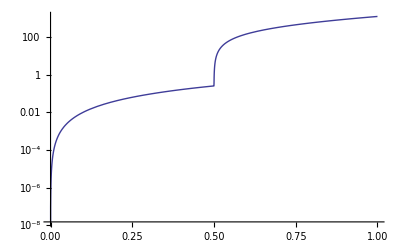

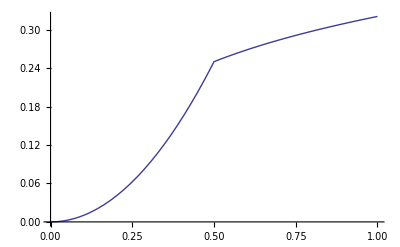

```mathematica
LogPlot[u[r]/.b->10^-3/.C->0.1,{r,0,1}]
Plot[u[r]/.b->10^3/.C->0.1,{r,0,1}]
```

```mathematica
D[β[x,y]D[u[x,y],x],x]+D[β[x,y]D[u[x,y],y],y]//PiecewiseExpand
```

4 (1+2 x^2+2 y^2)

```mathematica
u[1,0]
```

1/4 (1-9/(8 b))+3/(2 b)+C Log[2]

```mathematica
Luxy=Div[{{a[x,y] ,0},{0,b[x,y]}}.Grad[u[x,y],{x,y}, "Cartesian"],{x,y}, "Cartesian"]
Lurt=Div[{{a[r,θ] ,0},{0,b[r,θ]}}.Grad[u[r,θ],{r,θ}, "Polar"],{r,θ}, "Polar"]
Luxf=Div[{{a[ξ,φ] ,0},{0,b[ξ,φ]}}.Grad[u[ξ,φ],{ξ,φ}, "Elliptic"],{ξ,φ}, "Elliptic"]//Simplify
%==(Derivative[0,1][b][ξ,φ] Derivative[0,1][u][ξ,φ]+b[ξ,φ] Derivative[0,2][u][ξ,φ]+Derivative[1,0][a][ξ,φ] Derivative[1,0][u][ξ,φ]+a[ξ,φ] Derivative[2,0][u][ξ,φ])/(a^2(Sinh[ξ]^2+Sin[φ]^2))//Simplify
```

b^(0,1)[x,y] u^(0,1)[x,y]+b[x,y] u^(0,2)[x,y]+a^(1,0)[x,y] u^(1,0)[x,y]+a[x,y] u^(2,0)[x,y]

a^(1,0)[r,θ] u^(1,0)[r,θ]+((b^(0,1)[r,θ] u^(0,1)[r,θ])/r+(b[r,θ] u^(0,2)[r,θ])/r+a[r,θ] u^(1,0)[r,θ])/r+a[r,θ] u^(2,0)[r,θ]

-(2 (b^(0,1)[ξ,φ] u^(0,1)[ξ,φ]+b[ξ,φ] u^(0,2)[ξ,φ]+a^(1,0)[ξ,φ] u^(1,0)[ξ,φ]+a[ξ,φ] u^(2,0)[ξ,φ]))/(a^2 (Cos[2 φ]-Cosh[2 ξ]))

True

```mathematica
D[1/a[x,y],{x,2}]
```

(2 (a^(1,0)[x,y])^2)/a[x,y]^3-(a^(2,0)[x,y])/a[x,y]^2

```mathematica
Solve[(a Derivative[0,2][u][ξ,φ]+a Derivative[2,0][u][ξ,φ])/h[ξ,φ]^2==f[ξ,φ],Derivative[2,0][u][ξ,φ]]//Simplify
D[(f[ξ,φ] h[ξ,φ]^2)/a-Derivative[0,2][u][ξ,φ],ξ]//Simplify
D[(f[ξ,φ] h[ξ,φ]^2)/a-Derivative[0,2][u][ξ,φ],{ξ,2}]//Simplify
D[(f[ξ,φ] h[ξ,φ]^2)/a-Derivative[0,2][u][ξ,φ],φ]//Simplify
D[(f[ξ,φ] h[ξ,φ]^2)/a-Derivative[0,2][u][ξ,φ],{φ,2}]//Simplify
```

{{u^(2,0)[ξ,φ]→(f[ξ,φ] h[ξ,φ]^2)/a-u^(0,2)[ξ,φ]}}

(h[ξ,φ]^2 f^(1,0)[ξ,φ]+2 f[ξ,φ] h[ξ,φ] h^(1,0)[ξ,φ]-a u^(1,2)[ξ,φ])/a

(2 f[ξ,φ] (h^(1,0)[ξ,φ])^2+h[ξ,φ]^2 f^(2,0)[ξ,φ]+2 h[ξ,φ] (2 f^(1,0)[ξ,φ] h^(1,0)[ξ,φ]+f[ξ,φ] h^(2,0)[ξ,φ])-a u^(2,2)[ξ,φ])/a

(h[ξ,φ]^2 f^(0,1)[ξ,φ]+2 f[ξ,φ] h[ξ,φ] h^(0,1)[ξ,φ]-a u^(0,3)[ξ,φ])/a

(2 f[ξ,φ] (h^(0,1)[ξ,φ])^2+h[ξ,φ]^2 f^(0,2)[ξ,φ]+2 h[ξ,φ] (2 f^(0,1)[ξ,φ] h^(0,1)[ξ,φ]+f[ξ,φ] h^(0,2)[ξ,φ])-a u^(0,4)[ξ,φ])/a

```mathematica
Solve[(Derivative[0,1][b][ξ,φ] Derivative[0,1][u][ξ,φ]+b[ξ,φ] Derivative[0,2][u][ξ,φ]+Derivative[1,0][a][ξ,φ] Derivative[1,0][u][ξ,φ]+a[ξ,φ] Derivative[2,0][u][ξ,φ])/h[ξ,φ]^2-σ u[ξ,φ]==f[ξ,φ],Derivative[2,0][u][ξ,φ]]
D[(f[ξ,φ] h[ξ,φ]^2+σ h[ξ,φ]^2 u[ξ,φ]-Derivative[0,1][b][ξ,φ] Derivative[0,1][u][ξ,φ]-b[ξ,φ] Derivative[0,2][u][ξ,φ]-Derivative[1,0][a][ξ,φ] Derivative[1,0][u][ξ,φ])/a[ξ,φ],ξ]
Collect[%,{1/a[ξ,φ],1/a[ξ,φ]^2},FullSimplify]
(*Collect[%//FullSimplify,{u[ξ,φ],u^(0,1)[ξ,φ],u^(1,0)[ξ,φ],u^(1,1)[ξ,φ],u^(2,0)[ξ,φ],u^(2,1)[ξ,φ],u^(1,2)[ξ,φ],f[ξ,φ],f^(1,0)[ξ,φ] },FullSimplify]*)
(*D[,ξ]*)
```

{{u^(2,0)[ξ,φ]→(f[ξ,φ] h[ξ,φ]^2+σ h[ξ,φ]^2 u[ξ,φ]-b^(0,1)[ξ,φ] u^(0,1)[ξ,φ]-b[ξ,φ] u^(0,2)[ξ,φ]-a^(1,0)[ξ,φ] u^(1,0)[ξ,φ])/a[ξ,φ]}}

-(a^(1,0)[ξ,φ] (f[ξ,φ] h[ξ,φ]^2+σ h[ξ,φ]^2 u[ξ,φ]-b^(0,1)[ξ,φ] u^(0,1)[ξ,φ]-b[ξ,φ] u^(0,2)[ξ,φ]-a^(1,0)[ξ,φ] u^(1,0)[ξ,φ]))/a[ξ,φ]^2+1/a[ξ,φ](-u^(0,2)[ξ,φ] b^(1,0)[ξ,φ]+h[ξ,φ]^2 f^(1,0)[ξ,φ]+2 f[ξ,φ] h[ξ,φ] h^(1,0)[ξ,φ]+2 σ h[ξ,φ] u[ξ,φ] h^(1,0)[ξ,φ]+σ h[ξ,φ]^2 u^(1,0)[ξ,φ]-u^(0,1)[ξ,φ] b^(1,1)[ξ,φ]-b^(0,1)[ξ,φ] u^(1,1)[ξ,φ]-b[ξ,φ] u^(1,2)[ξ,φ]-u^(1,0)[ξ,φ] a^(2,0)[ξ,φ]-a^(1,0)[ξ,φ] u^(2,0)[ξ,φ])

(a^(1,0)[ξ,φ] (-h[ξ,φ]^2 (f[ξ,φ]+σ u[ξ,φ])+b^(0,1)[ξ,φ] u^(0,1)[ξ,φ]+b[ξ,φ] u^(0,2)[ξ,φ]+a^(1,0)[ξ,φ] u^(1,0)[ξ,φ]))/a[ξ,φ]^2+1/a[ξ,φ](-u^(0,2)[ξ,φ] b^(1,0)[ξ,φ]+2 h[ξ,φ] (f[ξ,φ]+σ u[ξ,φ]) h^(1,0)[ξ,φ]+h[ξ,φ]^2 (f^(1,0)[ξ,φ]+σ u^(1,0)[ξ,φ])-u^(0,1)[ξ,φ] b^(1,1)[ξ,φ]-b^(0,1)[ξ,φ] u^(1,1)[ξ,φ]-b[ξ,φ] u^(1,2)[ξ,φ]-u^(1,0)[ξ,φ] a^(2,0)[ξ,φ]-a^(1,0)[ξ,φ] u^(2,0)[ξ,φ])

```mathematica
CoordinateChartData["Elliptic", "ScaleFactors",{ξ,φ}]
```

CoordinateChartData::csysdim: Coordinate system "Elliptic" of metric "Euclidean" is not known in dimension 3.

CoordinateChartData[Elliptic,ScaleFactors,{f,ξ,φ}]

```mathematica
Grad[u[ξ,φ],{ξ,φ}, "Elliptic"]
2(Sinh[ξ]^2+Sin[φ]^2)==Cosh[2 ξ]-Cos[2 φ]//FullSimplify
```

{(√2 u^(1,0)[ξ,φ])/(a √(-Cos[2 φ]+Cosh[2 ξ])),(√2 u^(0,1)[ξ,φ])/(a √(-Cos[2 φ]+Cosh[2 ξ]))}

True

```mathematica
Div[{{r^2+1 ,0},{0,r^2+1}}.Grad[r^2,{r,θ}, "Polar"],{r,θ}, "Polar"]//Simplify
Div[{{x^2+y^2+1 ,0},{0,x^2+y^2+1}}.Grad[x^2+y^2,{x,y}, "Cartesian"],{x,y}, "Cartesian"]//Simplify
Div[{{b ,0},{0,b}}.Grad[1/4(1-1/(8b)-1/b)+1/b(r^4/2+r^2)+C Log[2r],{r,θ}, "Polar"],{r,θ}, "Polar"]//Simplify
Div[{{b,0},{0,b}}.Grad[1/4(1-1/(8b)-1/b)+1/b(((√(x^2+y^2))^4)/2+(√(x^2+y^2))^2)+C Log[2 √(x^2+y^2)],{x,y}, "Cartesian"],{x,y}, "Cartesian"]//Simplify
```

4+8 r^2

4+8 x^2+8 y^2

4+8 r^2

4+8 x^2+8 y^2

```mathematica
D[1/4(1-1/(8b)-1/b)+1/b(r^4/2+r^2)+C Log[2r],r]
```

C/r+(2 r+2 r^3)/b

```mathematica
Limit[1/4(1-1/(8b)-1/b)+1/b(r^4/2+r^2)+C Log[2r],r->0]
```

C (-∞)

```mathematica
Plot3D[8(x^2+y^2)+4,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Lurt=Div[{{a[r,θ] ,0},{0,b[r,θ]}}.Grad[u[r,θ],{r,θ}, "Polar"],{r,θ}, "Polar"]//Simplify
```

```mathematica
Solve[(Derivative[0,1][b][r,θ] Derivative[0,1][u][r,θ]+b[r,θ] Derivative[0,2][u][r,θ]+r (r Derivative[1,0][a][r,θ] Derivative[1,0][u][r,θ]+a[r,θ] (Derivative[1,0][u][r,θ]+r Derivative[2,0][u][r,θ])))/r^2==f[r,t],Derivative[2,0][u][r,θ]]
```

{{u^(2,0)[r,θ]→(r^2 f[r,t]-b^(0,1)[r,θ] u^(0,1)[r,θ]-b[r,θ] u^(0,2)[r,θ]-r a[r,θ] u^(1,0)[r,θ]-r^2 a^(1,0)[r,θ] u^(1,0)[r,θ])/(r^2 a[r,θ])}}

```mathematica
(r^2 f[r,t]-Derivative[0,1][b][r,θ] Derivative[0,1][u][r,θ]-b[r,θ] Derivative[0,2][u][r,θ]-r a[r,θ] Derivative[1,0][u][r,θ]-r^2 Derivative[1,0][a][r,θ] Derivative[1,0][u][r,θ])/(r^2 a[r,θ])==(f[r,t]-1/r^2(Derivative[0,1][b][r,θ] Derivative[0,1][u][r,θ]+b[r,θ] Derivative[0,2][u][r,θ])-Derivative[1,0][a][r,θ] Derivative[1,0][u][r,θ])/a[r,θ]-(Derivative[1,0][u][r,θ])/r//Simplify
```

True

```mathematica
Solve[Div[{{r^2+1 ,0},{0,r^2+1}}.Grad[u[r,θ],{r,θ}, "Polar"],{r,θ}, "Polar"]==8 r^2+4,Derivative[2,0][u][r,θ]]
```

{{u^(2,0)[r,θ]→(4 r^2+8 r^4-u^(0,2)[r,θ]-r^2 u^(0,2)[r,θ]-r u^(1,0)[r,θ]-3 r^3 u^(1,0)[r,θ])/(r^2 (1+r^2))}}

```mathematica
(4 r^2+8 r^4-Derivative[0,2][u][r,θ]-r^2 Derivative[0,2][u][r,θ]-r Derivative[1,0][u][r,θ]-3 r^3 Derivative[1,0][u][r,θ])/(r^2 (1+r^2))/.Derivative[0,2][u][r,θ]->0/.Derivative[1,0][u][r,θ]->2r//Simplify
```

2

```mathematica
8 r^2+4/.r->1/4//N
r^2+1/.r->1/4//N
2r/.r->1/4//N
```

4.5

1.0625

0.5

```mathematica
β[x_,y_]:=Piecewise[{{Subscript[b, in],x^2+4 y^2≤1},{Subscript[b, out],x^2+4 y^2>1}}]//PiecewiseExpand
u[x_,y_]:=Piecewise[{{x^2-y^2,x^2+4 y^2≤1},{Sin[x]Cos[y],x^2+4 y^2>1}}]//PiecewiseExpand
Div[{{β[x,y] ,0},{0,β[x,y]}}.Grad[u[x,y],{x,y}, "Cartesian"],{x,y}, "Cartesian"]//PiecewiseExpand
```

Piecewise[{{0, x^2+4 y^2≤1}, {-2 Cos[y] Sin[x] b_out, True}}]

```mathematica
u[x_,y_]:=Piecewise[{{x^2-y^2,x^2+4 y^2≤1},{Sin[x]Cos[y],x^2+4 y^2>1}}]//PiecewiseExpand
x=f  Cos[φ] Cosh[ξ]
y=f  Sin[φ] Sinh[ξ]
D[u[x,y],ξ]//PiecewiseExpand//FullSimplify
D[x^2-y^2,ξ]
```

f Cos[φ] Cosh[ξ]

f Sin[φ] Sinh[ξ]

Piecewise[{{f^2 Cos[2 φ] Sinh[2 ξ], f^2 (Cos[φ]^2 Cosh[ξ]^2+4 Sin[φ]^2 Sinh[ξ]^2)≤1}, {-f Cosh[ξ] Sin[φ] Sin[f Cos[φ] Cosh[ξ]] Sin[f Sin[φ] Sinh[ξ]]+f Cos[φ] Cos[f Cos[φ] Cosh[ξ]] Cos[f Sin[φ] Sinh[ξ]] Sinh[ξ], True}}]

2 f^2 Cos[φ]^2 Cosh[ξ] Sinh[ξ]-2 f^2 Cosh[ξ] Sin[φ]^2 Sinh[ξ]

```mathematica
|
```

```mathematica
f=1-1/4
Subscript[ξ, 0]=ArcCosh[1/f]
x=f  Cos[φ] Cosh[ξ]
y=f  Sin[φ] Sinh[ξ]
x^2-y^2
%//FullSimplify
Sin[x]Cos[y]/.ξ->Subscript[ξ, 0]
```

3/4

ArcCosh[4/3]

3/4 Cos[φ] Cosh[ξ]

3/4 Sin[φ] Sinh[ξ]

9/16 Cos[φ]^2 Cosh[ξ]^2-9/16 Sin[φ]^2 Sinh[ξ]^2

9/32 (1+Cos[2 φ] Cosh[2 ξ])

Cos[1/4 √7 Sin[φ]] Sin[Cos[φ]]

```mathematica
Div[{{Subscript[b, in] ,0},{0,Subscript[b, in]}}.Grad[x^2-y^2,{x,y}, "Cartesian"],{x,y}, "Cartesian"]//Simplify
Div[{{Subscript[b, out],0},{0,Subscript[b, out]}}.Grad[Sin[x]Cos[y],{x,y}, "Cartesian"],{x,y}, "Cartesian"]//Simplify
```

0

-2 Cos[y] Sin[x] b_out

```mathematica
Sin[f Cosh[ξ]Cos[ϕ]]//TrigExpand
```

```mathematica
F=-2β Sin[a  Cos[φ] Cosh[ξ]]Cos[a  Sin[φ] Sinh[ξ]]
D[F,ξ]//FullSimplify/.{a Sin[φ] Sinh[ξ]}->x
D[F,φ]//FullSimplify
(*Grad[F,{ξ,φ}, "Elliptic"]//FullSimplify*)
```

-2 β Cos[a Sin[φ] Sinh[ξ]] Sin[a Cos[φ] Cosh[ξ]]

2 a β (Cosh[ξ] Sin[φ] Sin[a Cos[φ] Cosh[ξ]] Sin[a Sin[φ] Sinh[ξ]]-Cos[φ] Cos[a Cos[φ] Cosh[ξ]] Cos[a Sin[φ] Sinh[ξ]] Sinh[ξ])

2 a β (Cos[a Cos[φ] Cosh[ξ]] Cos[a Sin[φ] Sinh[ξ]] Cosh[ξ] Sin[φ]+Cos[φ] Sin[a Cos[φ] Cosh[ξ]] Sin[a Sin[φ] Sinh[ξ]] Sinh[ξ])

{(2 √2 β (Cosh[ξ] Sin[φ] Sin[a Cos[φ] Cosh[ξ]] Sin[a Sin[φ] Sinh[ξ]]-Cos[φ] Cos[a Cos[φ] Cosh[ξ]] Cos[a Sin[φ] Sinh[ξ]] Sinh[ξ]))/(√(-Cos[2 φ]+Cosh[2 ξ])),(2 √2 β (Cos[a Cos[φ] Cosh[ξ]] Cos[a Sin[φ] Sinh[ξ]] Cosh[ξ] Sin[φ]+Cos[φ] Sin[a Cos[φ] Cosh[ξ]] Sin[a Sin[φ] Sinh[ξ]] Sinh[ξ]))/(√(-Cos[2 φ]+Cosh[2 ξ]))}

```mathematica
2  β (a Cosh[ξ] Sin[φ] Sin[x] Sin[y]-Cos[x] Cos[y] a Cos[φ] Sinh[ξ])
2 β (Cos[x] Cos[y] a Cosh[ξ] Sin[φ]+Sin[x] Sin[y]Cos[φ]  Sinh[ξ])
```

```mathematica
F=-2β Sin[x[ξ,φ]]Cos[y[ξ,φ]]
Fn=D[F,ξ]
Ff= D[F,φ]
D[F,{ξ,2}]//FullSimplify
(*D[F,{ξ,2}]==F (x^(1,0)[ξ,φ])^2+*)
D[F,{φ,2}]//FullSimplify
```

-2 β Cos[y[ξ,φ]] Sin[x[ξ,φ]]

-2 β Cos[x[ξ,φ]] Cos[y[ξ,φ]] x^(1,0)[ξ,φ]+2 β Sin[x[ξ,φ]] Sin[y[ξ,φ]] y^(1,0)[ξ,φ]

-2 β Cos[x[ξ,φ]] Cos[y[ξ,φ]] x^(0,1)[ξ,φ]+2 β Sin[x[ξ,φ]] Sin[y[ξ,φ]] y^(0,1)[ξ,φ]

2 β (Cos[x[ξ,φ]] (2 Sin[y[ξ,φ]] x^(1,0)[ξ,φ] y^(1,0)[ξ,φ]-Cos[y[ξ,φ]] x^(2,0)[ξ,φ])+Sin[x[ξ,φ]] (Cos[y[ξ,φ]] ((x^(1,0)[ξ,φ])^2+(y^(1,0)[ξ,φ])^2)+Sin[y[ξ,φ]] y^(2,0)[ξ,φ]))

2 β (Cos[x[ξ,φ]] (2 Sin[y[ξ,φ]] x^(0,1)[ξ,φ] y^(0,1)[ξ,φ]-Cos[y[ξ,φ]] x^(0,2)[ξ,φ])+Sin[x[ξ,φ]] (Cos[y[ξ,φ]] ((x^(0,1)[ξ,φ])^2+(y^(0,1)[ξ,φ])^2)+Sin[y[ξ,φ]] y^(0,2)[ξ,φ]))

```mathematica
x=a  Cos[φ] Cosh[ξ]
y=a  Sin[φ] Sinh[ξ]
xn=D[x,ξ]
yn=D[y,ξ]
D[x^2-y^2,ξ]==2x xn-2y yn//Simplify
(*D[y,{ξ,2}]==y//Simplify
D[y,φ]
D[y,{φ,2}]==-y*)
```

a Cos[φ] Cosh[ξ]

a Sin[φ] Sinh[ξ]

a Cos[φ] Sinh[ξ]

a Cosh[ξ] Sin[φ]

True

```mathematica
Sin[x[ξ,φ]]Cos[y[ξ,φ]]
D[%,ξ]
x[ξ,φ]^2+y[ξ,φ]^2
D[%,ξ]
```

Cos[y[ξ,φ]] Sin[x[ξ,φ]]

Cos[x[ξ,φ]] Cos[y[ξ,φ]] x^(1,0)[ξ,φ]-Sin[x[ξ,φ]] Sin[y[ξ,φ]] y^(1,0)[ξ,φ]

x[ξ,φ]^2+y[ξ,φ]^2

2 x[ξ,φ] x^(1,0)[ξ,φ]+2 y[ξ,φ] y^(1,0)[ξ,φ]

```mathematica
y=.
```

```mathematica
Div[{{a[x,y] ,b[x,y]},{c[x,y],d[x,y]}}.Grad[u[x,y],{x,y}, "Cartesian"],{x,y}, "Cartesian"]//FullSimplify
Div[{{a[x,y] ,0},{0,b[x,y]}}.Grad[u[x,y],{x,y}, "Cartesian"],{x,y}, "Cartesian"]//FullSimplify
Div[c[x,y,t]Grad[u[x,y],{x,y}, "Cartesian"],{x,y}, "Cartesian"]//FullSimplify
```

d[x,y] u^(0,2)[x,y]+u^(0,1)[x,y] (d^(0,1)[x,y]+b^(1,0)[x,y])+(c^(0,1)[x,y]+a^(1,0)[x,y]) u^(1,0)[x,y]+(b[x,y]+c[x,y]) u^(1,1)[x,y]+a[x,y] u^(2,0)[x,y]

b^(0,1)[x,y] u^(0,1)[x,y]+b[x,y] u^(0,2)[x,y]+a^(1,0)[x,y] u^(1,0)[x,y]+a[x,y] u^(2,0)[x,y]

c[x,y,t] (u^(0,2)[x,y]+u^(2,0)[x,y])+u^(0,1)[x,y] c^(0,1,0)[x,y,t]+u^(1,0)[x,y] c^(1,0,0)[x,y,t]

```mathematica
u[x_,y_]:=Piecewise[{{x^2-y^2,x^2+4 y^2≤1},{Sin[x]Cos[y],x^2+4 y^2>1}}]//PiecewiseExpand
Plot3D[u[x,y],{x,-1.1,1.1},{y,-1.1,1.1}]
```

-Graphics3D-